```mathematica
(* chap1-3 *)
(* 1.18 *)
```

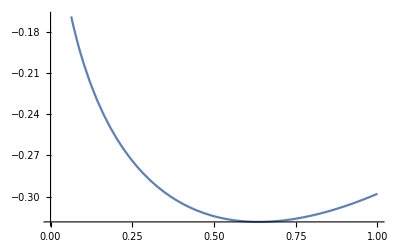

```mathematica
Plot[a/2-Sqrt[2 a/Pi],{a,0,1}]
```

```mathematica
(* 1.19 *)
Laplacian[E^(-a r^2),{r,theta,phi},"Spherical"]
```

-6 a ⅇ^(-a r^2)+4 a^2 ⅇ^(-a r^2) r^2

```mathematica
(* 1.20 *)
t=(1/2) ArcTan[2 o12/(o11-o22)];
omega=FullSimplify[TrigReduce[o11 Cos[t]^2+2 o12 Cos[t] Sin[t]+o22 Sin[t]^2]]
```

1/2 (o11+o11 √(1+(4 o12^2)/(o11-o22)^2)+o22-√(1+(4 o12^2)/(o11-o22)^2) o22)

```mathematica
(* 1.22 *)
s[r_]:=(1/Sqrt[Pi]) E^(-r);
pz[r_,th_]:=(1/Sqrt[32 Pi]) r E^(-r/2) Cos[th];
h11=-1/2+2Pi Integrate[s[r] r Cos[th] s[r]  r^2 Sin[th],{r,0,Infinity},{th,0,Pi}]
```

-1/2

```mathematica
h12=F*2Pi Integrate[s[r] r Cos[th] pz[r,th]  r^2 Sin[th],{r,0,Infinity},{th,0,Pi}]
```

(128 √2 F)/243

```mathematica
h22=-1/8+2Pi Integrate[pz[r,th] r Cos[th] pz[r,th]  r^2 Sin[th],{r,0,Infinity},{th,0,Pi}]
```

-1/8

```mathematica
p=(1/2) ArcTan[2 h12 /(h11-h22)]
```

-1/2 ArcTan[(2048 √2 F)/729]

```mathematica
e=FullSimplify[TrigReduce[h11 Cos[p]^2+h12 Sin[2p]+h22 Sin[p]^2]]
```

-5/16-(√(531441+8388608 F^2))/3888

```mathematica
ee=Series[e,{F,0,4}]
```

-1/2-(262144 F^2)/177147+(549755813888 F^4)/94143178827+O[F]^5

```mathematica
een=N[%]
```

-0.5-1.47981 (F+0.)^2+5.83957 (F+0.)^4+O[F+0.]^5

```mathematica
alpha=1.47981*2
```

2.95962